```mathematica
Pulse[θ_]:=({{Cos[θ/2], -ⅈ Sin[θ/2]}, {-ⅈ Sin[θ/2], Cos[θ/2]}});
Prop[θ_]:=({{Exp[-ⅈ θ/2], 0}, {0, Exp[ⅈ θ/2]}});
Mirror = ({{0, 1}, {1, 0}});

finalState = Pulse[θ2].Prop[ϕ].Pulse[θ1].({{0}, {1}});
MatrixForm@finalState
```

(-ⅈ ⅇ^(-(ⅈ ϕ)/2) Cos[θ2/2] Sin[θ1/2]-ⅈ ⅇ^((ⅈ ϕ)/2) Cos[θ1/2] Sin[θ2/2]
ⅇ^((ⅈ ϕ)/2) Cos[θ1/2] Cos[θ2/2]-ⅇ^(-(ⅈ ϕ)/2) Sin[θ1/2] Sin[θ2/2])

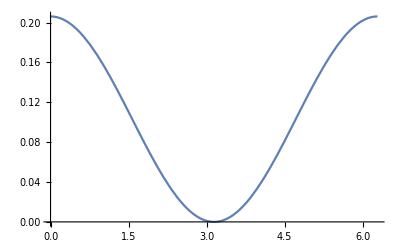

```mathematica
Plot[
Abs[{{1,0}}.finalState]^2//.{ϕ-> x, θ2-> 0.3 π/2, θ1->0.3 π/2},
{x,0,2 π}
]
```

```mathematica
FullSimplify[Abs[{{1,0}}.finalState]^2,
Assumptions->{{θ1, θ2, ϕ}∈ Reals}
]
```

{{Abs[Cos[θ2/2] Sin[θ1/2]+ⅇ^(ⅈ ϕ) Cos[θ1/2] Sin[θ2/2]]^2}}

{1/2 (1-Cos[θ1] Cos[θ2]+Cos[ϕ] Sin[θ1] Sin[θ2])}

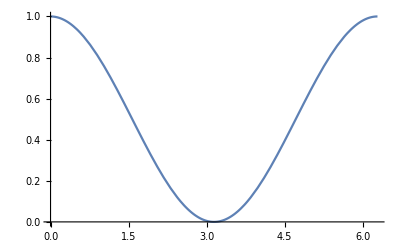

```mathematica
a = ({{1,0}}.finalState)[[1]];
b =FullSimplify[a * Conjugate[a],
Assumptions->{{θ1, θ2, ϕ}∈ Reals}
]
Plot[
b//.{ϕ-> x, θ2->  π/2, θ1->π/2},
{x,0,2 π}
]
```